```mathematica
nodes={
	{0,100},{45,100},{75,100},{100,100},
	{0,85},{45,60},{65,65},{100,70},
	{0,35},{35,35},{70,30},{100,40},
	{0,0},{40,0},{80,0},{100,0}
};
nodesG={{0,100,1},{45,100,1},{75,100,1},{100,100,1},{0,85,1},{45,60,1},{65,65,1},{100,70,1},{0,35,1},{35,35,1},{70,30,1},{100,40,1},{0,0,1},{40,0,1},{80,0,1},{100,0,1}};
nodesH={{0,100,0},{45,100,0},{75,100,0},{100,100,0},{0,85,0},{45,60,0},{65,65,0},{100,70,0},{0,35,0},{35,35,0},{70,30,0},{100,40,0},{0,0,0},{40,0,0},{80,0,0},{100,0,0}};
nodesMidG={nodesG[[6]],nodesG[[7]],nodesG[[10]],nodesG[[11]]};
nodesMidH={nodesH[[6]],nodesH[[7]],nodesH[[10]],nodesH[[11]]};
lines={
	Line[{nodes[[5]],nodes[[6]],nodes[[7]],nodes[[8]]}],
	Line[{nodes[[9]],nodes[[10]],nodes[[11]],nodes[[12]]}],
	Line[{nodes[[13]],nodes[[14]],nodes[[15]],nodes[[16]],
		nodes[[12]],nodes[[8]],nodes[[4]],nodes[[3]],nodes[[2]],nodes[[1]],nodes[[5]],nodes[[9]],nodes[[13]]}],
	Line[{nodes[[2]],nodes[[6]],nodes[[10]],nodes[[14]]}],
	Line[{nodes[[3]],nodes[[7]],nodes[[11]],nodes[[15]]}]
};
floorLines={
	Line[{nodesH[[5]],nodesH[[6]],nodesH[[7]],nodesH[[8]]}],
	Line[{nodesH[[9]],nodesH[[10]],nodesH[[11]],nodesH[[12]]}],
	Line[{nodesH[[13]],nodesH[[14]],nodesH[[15]],nodesH[[16]],
		nodesH[[12]],nodesH[[8]],nodesH[[4]],nodesH[[3]],nodesH[[2]],nodesH[[1]],nodesH[[5]],nodesH[[9]],nodesH[[13]]}],
	Line[{nodesH[[2]],nodesH[[6]],nodesH[[10]],nodesH[[14]]}],
	Line[{nodesH[[3]],nodesH[[7]],nodesH[[11]],nodesH[[15]]}]
};
ceilingLines={
	Line[{nodesG[[5]],nodesG[[6]],nodesG[[7]],nodesG[[8]]}],
	Line[{nodesG[[9]],nodesG[[10]],nodesG[[11]],nodesG[[12]]}],
	Line[{nodesG[[13]],nodesG[[14]],nodesG[[15]],nodesG[[16]],
		nodesG[[12]],nodesG[[8]],nodesG[[4]],nodesG[[3]],nodesG[[2]],nodesG[[1]],nodesG[[5]],nodesG[[9]],nodesG[[13]]}],
	Line[{nodesG[[2]],nodesG[[6]],nodesG[[10]],nodesG[[14]]}],
	Line[{nodesG[[3]],nodesG[[7]],nodesG[[11]],nodesG[[15]]}]
};
g[x_,y_,x0_,y0_,σ_]:=Exp[-((x-x0)^2+(y-y0)^2)/(2 σ^2)]    (* Custom 2D Gaussian *)
nXYGridLines=5;
xYGridLines=Table[{100/(nXYGridLines-1) i,Thickness[0.002]} , {i,0,nXYGridLines-1}];
nXZGridLines=3;
xZGridLines=Table[{1/(nXZGridLines-1) i,Thickness[0.002] }, {i,0,nXZGridLines-1}];
nZXGridLines=5;
zXGridLines=Table[{100/(nZXGridLines-1) i,Directive[Thickness[0.003],Black]}, {i,0,nZXGridLines-1}] ;    (* Grid line positions and their individual stylings for the lower plate on the 3D plot. *)
plotVisuals={Lighting["Neutral"],Specularity[White,70],Opacity[0.6]};
```

```mathematica
SetOptions[Plot3D,
	Mesh->None,
	AxesLabel->None,
	PlotRange->{{0,100},{0,100},{0,1}},
	PlotPoints->{100,100},
	LabelStyle->{FontFamily["DejaVu Math TeX Gyre"],Directive[20,Bold]},
	Ticks->None,
	Boxed->False
];
opacity = 0.6;
meshLineThickness=0.0035;
meshColors={Gray,Gray,Gray,Gray};
sufaceColors={Darker[Red],Blue,Green,Darker[Yellow]};

Show[
	Plot3D[
		g[x,y,nodes[[2,2,1]],nodes[[2,2,2]],10],
		{x,nodes[[2,2,1]]-2.7 10,nodes[[2,2,1]]+2.7 10},
		{y,nodes[[2,2,2]]-2.7 10,nodes[[2,2,2]]+2.7 10},
		PlotStyle->Directive[RGBColor["#ff8e8e"],plotVisuals],
		(*MeshShading->{{{sufaceColors[[1]],Opacity[opacity]},{sufaceColors[[1]],Opacity[opacity]}},{{sufaceColors[[1]],Opacity[opacity]},{sufaceColors[[1]],Opacity[opacity]}}},
		MeshStyle->{{Thickness[meshLineThickness],meshColors[[1]]}},*)
		RegionFunction->Function[{x,y,z},(x-nodes[[2,2,1]])^2+(y-nodes[[2,2,2]])^2<27^2]
	],
	Plot3D[
		g[x,y,nodes[[2,3,1]],nodes[[2,3,2]],10],
		{x,nodes[[2,3,1]]-2.7 10,nodes[[2,3,1]]+2.7 10},
		{y,nodes[[2,3,2]]-2.7 10,nodes[[2,3,2]]+2.7 10},
		PlotStyle->Directive[RGBColor["#8beb91"],plotVisuals],
		(*MeshShading->{{{sufaceColors[[2]],Opacity[opacity]},{sufaceColors[[2]],Opacity[opacity]}},{{sufaceColors[[2]],Opacity[opacity]},{sufaceColors[[2]],Opacity[opacity]}}},
		MeshStyle->{{Thickness[meshLineThickness],meshColors[[2]]}},*)
		RegionFunction->Function[{x,y,z},(x-nodes[[2,3,1]])^2+(y-nodes[[2,3,2]])^2<27^2]
	],
	Plot3D[
		g[x,y,nodes[[3,2,1]],nodes[[3,2,2]],12],
		{x,nodes[[3,2,1]]-2.7 12,nodes[[3,2,1]]+2.7 12},
		{y,nodes[[3,2,2]]-2.7 12,nodes[[3,2,2]]+2.7 12},
		PlotStyle->Directive[RGBColor["#66aaf6"],plotVisuals],
		(*MeshShading->{{{sufaceColors[[3]],Opacity[opacity]},{sufaceColors[[3]],Opacity[opacity]}},{{sufaceColors[[3]],Opacity[opacity]},{sufaceColors[[3]],Opacity[opacity]}}},
		MeshStyle->{{Thickness[meshLineThickness],meshColors[[3]]}},*)
		RegionFunction->Function[{x,y,z},(x-nodes[[3,2,1]])^2+(y-nodes[[3,2,2]])^2<(2.7 12)^2]
	],
	Plot3D[
		g[x,y,nodes[[3,3,1]],nodes[[3,3,2]],11],
		{x,nodes[[3,3,1]]-2.7 11,nodes[[3,3,1]]+2.7 11},
		{y,nodes[[3,3,2]]-2.7 11,nodes[[3,3,2]]+2.7 11},
		PlotStyle->Directive[RGBColor["#d5d87d"],plotVisuals],
		(*MeshShading->{{{sufaceColors[[4]],Opacity[opacity]},{sufaceColors[[4]],Opacity[opacity]}},{{sufaceColors[[4]],Opacity[opacity]},{sufaceColors[[4]],Opacity[opacity]}}},
		MeshStyle->{{Thickness[meshLineThickness],meshColors[[4]]}},*)
		RegionFunction->Function[{x,y,z},(x-nodes[[3,3,1]])^2+(y-nodes[[3,3,2]])^2<(2.7 11)^2]
	],
	Graphics3D[{
		Red,PointSize[0.03],Thickness[0.009],
		Table[Line[{nodesMidH[[i]],nodesMidG[[i]]}],{i,1,Length[nodesMidG]}],
		Point[nodesH],
		Black,Thickness[0.009],Specularity[White,70],
		floorLines,
		LightBlue, Opacity[0.1],
		Hyperplane[{1,0,0},{0,0,0}],
		Hyperplane[{0,-1,0},{0,100,0}],
		RGBColor["#a4f2f1"], Opacity[0.5],
		Hyperplane[{0,0,1},{0,0,0}]
	}],
	ImageSize->600,
	FaceGrids->{
			{{-1,0,0},{xYGridLines,xZGridLines}},
			{{0,1,0},{xYGridLines,xZGridLines}}(*,
			{{0,0,-1},{zXGridLines,zXGridLines}}*)
	}
]
```

-Graphics3D-

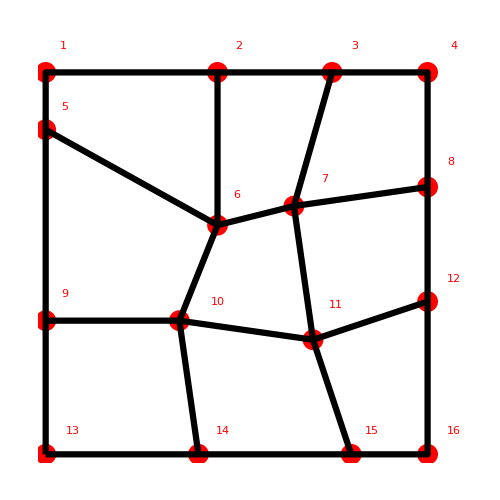

```mathematica
Graphics[{
	Red,PointSize[0.03],
	Point[nodes],
	Black,Thickness[0.009],
	lines,
	FontSize->36,Red,
	Text[13,{7,6}], Text[14,{46.5,6}], Text[15,{85.5,6}],Text[16,{107,6}],
	Text[9,{5,42}],Text[10,{45,40}],Text[11,{76,39}],Text[12,{107,46}],
	Text[5,{5,91}],Text[6,{50,68}],Text[7,{73,72}],Text[8,{106,76.5}],
	Text[1,{4.5,107}],Text[2,{50.5,107}],Text[3,{81,107}],Text[4,{107,107}]
},ImageSize->500]
```